```mathematica
ClearAll["Global`*"]
epi:=1
mu:=1
r:=.8
i:=I
(*odd term*)
G1:={-i*w* r,-kz,0,w* mu,0,0}
G2:={kz,i *w *r,-k,0,- w *mu,0}
G3:={0,k,i *w *r,0,0,-w *mu}
G4:={w *epi,0,0,i *w* r,-kz,0}
G5:={0,-w* epi,0,-kz,-i *w* r,k}
G6:={0 ,0,w *epi,0,k,i *w *r}
G:={G1,G2,G3,G4,G5,G6}
G//MatrixForm;
g:=Det[G]
g
Factor[g]
wa:=0
wb:=2
ka:=0
kb:=10
kza:=0
kzb:=5
(*even terms*)
F1:={-i*w*r,-kz,0,w*mu,0,0}
F2:={kz,i*w*r,k,0,-w*mu,0}
F3:={0,-k,i*w*r,0,0,-w*mu}
F4:={w*epi,0,0,i*w*r,-kz,0}
F5:={0,w*epi,0,kz,i*w*r,k}
F6:={0,0,w*epi,0,-k,i*w*r}
F:={F1,F2,F3,F4,F5,F6}
F//MatrixForm;
f:=Det[F]
Factor[f]
ContourPlot3D[g/(w)==0,{w,wa,wb},{k,ka,kb},{kz,kza,kzb}]
ContourPlot3D[f/(w)==0,{w,wa,wb},{k,ka,kb},{kz,kza,kzb},ContourStyle->Directive[Red,Specularity[White,20]]]
```

0.36 k^4 w^2+0. k^2 kz^2 w^2-0.36 kz^4 w^2-1.1808 k^2 w^4+0. kz^2 w^4+0.046656 w^6

0.36 (1. k^4 w^2-1. kz^4 w^2-3.28 k^2 w^4+0.1296 w^6)

-0.36 (1. k^4 w^2-1. kz^4 w^2-3.28 k^2 w^4+0.1296 w^6)

-Graphics3D-

-Graphics3D-

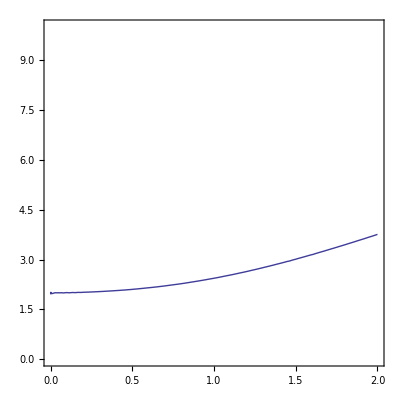

```mathematica
kz:=2(*檢查用*)
ContourPlot[g/(w)==0,{w,wa,wb},{k,ka,kb}]
```